```mathematica
Yt = (Yt1/v)/((Yt1/v)^4+q)-(Yt2/v)/((Yt2/v)^4+q)+(k+1)/3*((1-s)*(Yt2-Yt5)+s*(Yt3-Yt6))+(1-s)Yt2+s Yt3
```

Yt1/(v (q+Yt1^4/v^4))+(1-s) Yt2-Yt2/(v (q+Yt2^4/v^4))+s Yt3+1/3 (1+k) ((1-s) (Yt2-Yt5)+s (Yt3-Yt6))

```mathematica
J = {{dYt,dAt,dBt,dCt,dDt,dEt},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0}}
```

{{dYt,dAt,dBt,dCt,dDt,dEt},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0}}

dt is 0 as growth is not dependent on the 4-year time lag of growth

```mathematica
dCt = 0
```

```mathematica
D[Yt,Yt1]
D[Yt,Yt2]
D[Yt,Yt3]
D[Yt,Yt4]
D[Yt,Yt5]
D[Yt,Yt6]
```

-(4 Yt1^4)/(v^5 (q+Yt1^4/v^4)^2)+1/(v (q+Yt1^4/v^4))

1+1/3 (1+k) (1-s)-s+(4 Yt2^4)/(v^5 (q+Yt2^4/v^4)^2)-1/(v (q+Yt2^4/v^4))

s+1/3 (1+k) s

0

1/3 (1+k) (-1+s)

-1/3 (1+k) s

```mathematica
J=({{dYt, dAt, s+s/3(1+k), 0, (k+1)/3(s-1), -(k+1)/3 s}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}})
```

{{dYt,dAt,s+1/3 (1+k) s,0,1/3 (1+k) (-1+s),1/3 (-1-k) s},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0}}

```mathematica
MatrixForm[J]
```

(dYt | dAt | s+1/3 (1+k) s | 0 | 1/3 (1+k) (-1+s) | 1/3 (-1-k) s
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

```mathematica
s = 0.6
k=0.3
v=500
q=0.001
```

0.6

0.3

500

0.001

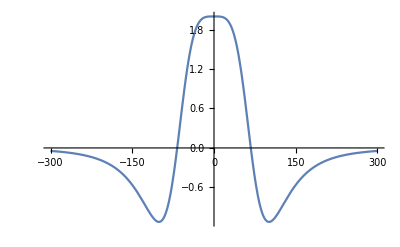

```mathematica
Plot[-(4 Yt1^4)/(v^5 (q+Yt1^4/v^4)^2)+1/(v (q+Yt1^4/v^4)),{Yt1,-300, 300}]
```

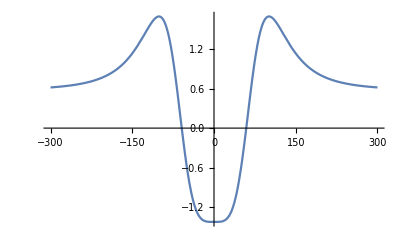

```mathematica
Plot[1+1/3 (1+k) (1-s)-s+(4 Yt2^4)/(v^5 (q+Yt2^4/v^4)^2)-1/(v (q+Yt2^4/v^4)),{Yt2,-300, 300}]
```